```mathematica
(*First we curve-fit Pfail as a function of p and L, in accordance with (A1) of Watson and Barrett (2014)*)
SetDirectory[NotebookDirectory[]];
s=Import["k9.csv"]
sNames=s[[1]]
sData=s[[2;;]]
```

{{Code,p,I_{tot},P_{fail,tot}},{9C3,2,0.01,0.130216,0.0212755},{9C3,2,0.02,0.363609,0.0789604},{9C3,2,0.03,0.618589,0.162438},{9C3,2,0.04,0.857152,0.260432},{9C3,2,0.05,1.06496,0.364335},{C9,4,0.01,0.0685862,0.0099234},{C9,4,0.02,0.177667,0.0397169},{C9,4,0.03,0.165948,0.0889478},{C9,4,0.04,0.521695,0.157495},{C9,4,0.05,0.680323,0.24252},{9C5,2,0.01,0.0262211,0.00249832},{9C5,2,0.02,0.137653,0.0193118},{9C5,2,0.03,0.343579,0.0605155},{9C5,2,0.04,0.596801,0.131512},{9C5,2,0.05,0.846046,0.228925},{2C7,3+C11,2,0.01,0.0737781,0.00875226},{2C7,3+C11,2,0.02,0.219448,0.0351371},{2C7,3+C11,2,0.03,0.466724,0.0825427},{2C7,3+C11,2,0.04,0.585292,0.141191},{2C7,3+C11,2,0.05,0.569889,0.221291}}

{Code,p,I_{tot},P_{fail,tot}}

{{9C3,2,0.01,0.130216,0.0212755},{9C3,2,0.02,0.363609,0.0789604},{9C3,2,0.03,0.618589,0.162438},{9C3,2,0.04,0.857152,0.260432},{9C3,2,0.05,1.06496,0.364335},{C9,4,0.01,0.0685862,0.0099234},{C9,4,0.02,0.177667,0.0397169},{C9,4,0.03,0.165948,0.0889478},{C9,4,0.04,0.521695,0.157495},{C9,4,0.05,0.680323,0.24252},{9C5,2,0.01,0.0262211,0.00249832},{9C5,2,0.02,0.137653,0.0193118},{9C5,2,0.03,0.343579,0.0605155},{9C5,2,0.04,0.596801,0.131512},{9C5,2,0.05,0.846046,0.228925},{2C7,3+C11,2,0.01,0.0737781,0.00875226},{2C7,3+C11,2,0.02,0.219448,0.0351371},{2C7,3+C11,2,0.03,0.466724,0.0825427},{2C7,3+C11,2,0.04,0.585292,0.141191},{2C7,3+C11,2,0.05,0.569889,0.221291}}

{{{0.01,0.130216},{0.02,0.363609},{0.03,0.618589},{0.04,0.857152},{0.05,1.06496}},{{0.01,0.0685862},{0.02,0.177667},{0.03,0.165948},{0.04,0.521695},{0.05,0.680323}},{{0.01,0.0262211},{0.02,0.137653},{0.03,0.343579},{0.04,0.596801},{0.05,0.846046}},{{0.01,0.0737781},{0.02,0.219448},{0.03,0.466724},{0.04,0.585292},{0.05,0.569889}}}

{{{0.01,0.0212755},{0.02,0.0789604},{0.03,0.162438},{0.04,0.260432},{0.05,0.364335}},{{0.01,0.0099234},{0.02,0.0397169},{0.03,0.0889478},{0.04,0.157495},{0.05,0.24252}},{{0.01,0.00249832},{0.02,0.0193118},{0.03,0.0605155},{0.04,0.131512},{0.05,0.228925}},{{0.01,0.00875226},{0.02,0.0351371},{0.03,0.0825427},{0.04,0.141191},{0.05,0.221291}}}

{{{0.01,0.130216},{0.02,0.363609},{0.03,0.618589},{0.04,0.857152},{0.05,1.06496}},{{0.01,0.0685862},{0.02,0.177667},{0.03,0.165948},{0.04,0.521695},{0.05,0.680323}}}

{{{0.01,0.0262211},{0.02,0.137653},{0.03,0.343579},{0.04,0.596801},{0.05,0.846046}},{{0.01,0.0737781},{0.02,0.219448},{0.03,0.466724},{0.04,0.585292},{0.05,0.569889}}}

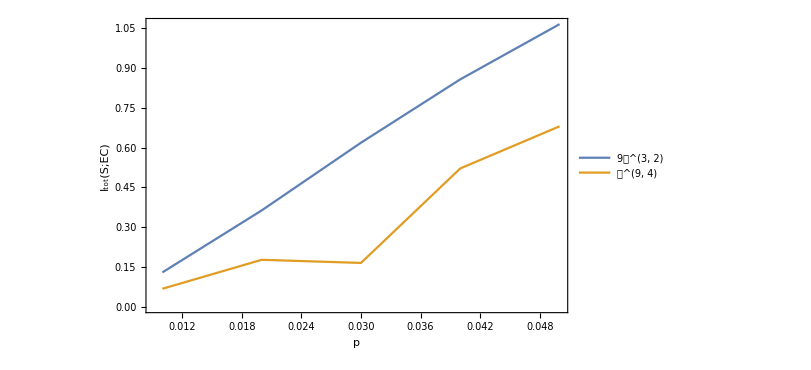

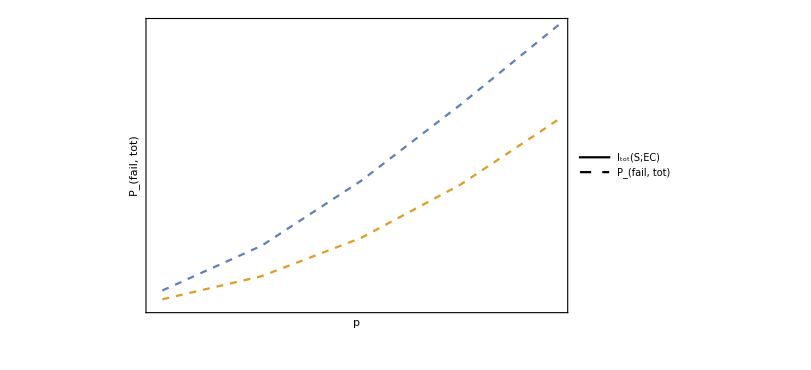

-Graphics--Graphics-

k9.pdf

{{{0.01,0.130216},{0.02,0.363609},{0.03,0.618589},{0.04,0.857152},{0.05,1.06496}},{{0.01,0.0685862},{0.02,0.177667},{0.03,0.165948},{0.04,0.521695},{0.05,0.680323}},{{0.01,0.0262211},{0.02,0.137653},{0.03,0.343579},{0.04,0.596801},{0.05,0.846046}},{{0.01,0.0737781},{0.02,0.219448},{0.03,0.466724},{0.04,0.585292},{0.05,0.569889}}}

{{{0.01,0.0212755},{0.02,0.0789604},{0.03,0.162438},{0.04,0.260432},{0.05,0.364335}},{{0.01,0.0099234},{0.02,0.0397169},{0.03,0.0889478},{0.04,0.157495},{0.05,0.24252}},{{0.01,0.00249832},{0.02,0.0193118},{0.03,0.0605155},{0.04,0.131512},{0.05,0.228925}},{{0.01,0.00875226},{0.02,0.0351371},{0.03,0.0825427},{0.04,0.141191},{0.05,0.221291}}}

{{{0.01,0.130216},{0.02,0.363609},{0.03,0.618589},{0.04,0.857152},{0.05,1.06496}},{{0.01,0.0685862},{0.02,0.177667},{0.03,0.165948},{0.04,0.521695},{0.05,0.680323}}}

{{{0.01,0.0262211},{0.02,0.137653},{0.03,0.343579},{0.04,0.596801},{0.05,0.846046}},{{0.01,0.0737781},{0.02,0.219448},{0.03,0.466724},{0.04,0.585292},{0.05,0.569889}}}

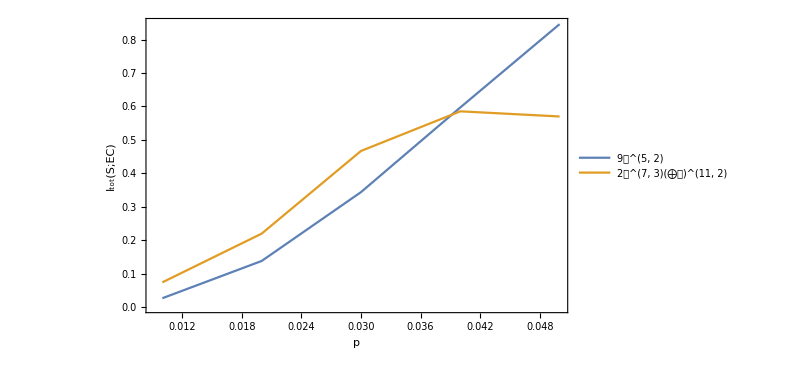

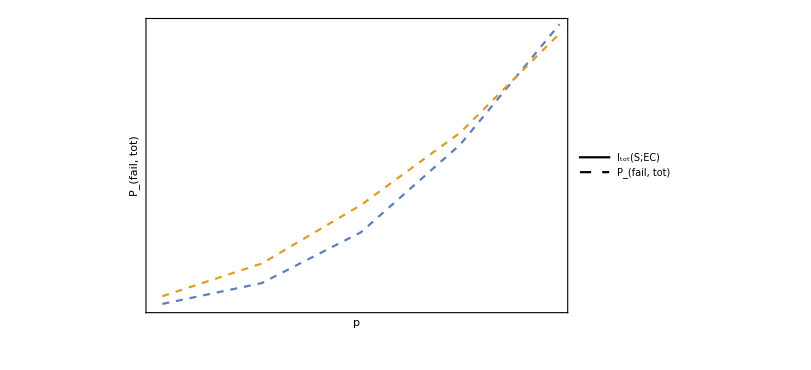

-Graphics--Graphics-

k9_2.pdf

```mathematica
DataPlot=Partition[Transpose[{sData[[;;,2]],sData[[;;,3]]}],5]
DataPlotPfail=Partition[Transpose[{sData[[;;,2]],sData[[;;,4]]}],5]
dataI1=DataPlot[[1;;2,;;]]
dataI2=DataPlot[[3;;4,;;]]
plot1=ListLinePlot[DataPlot[[1;;2,;;]],Frame->{True,True,True,False},ImagePadding->50,PlotLegends->Placed[LineLegend[{"9𝒞^(3, 2)","𝒞^(9, 4)"}],{0.1,0.8}],FrameLabel->{{"I_tot(S;EC)",None},{"p",None}},ImageSize->600]
plot2=ListLinePlot[DataPlotPfail[[1;;2,;;]],AxesLabel->{"p","P_(fail, tot)"},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},ImagePadding->50,PlotStyle->Dashed,FrameLabel->{{None,"P_(fail, tot)"},{None,None}},PlotLegends->Placed[LineLegend[{Black,{Dashed,Black}},{"I_tot(S;EC)","P_(fail, tot)"}],{0.12,0.6}],ImageSize->600] 
plot3=Overlay[{plot1,plot2}]
Export["k9.pdf",plot3]

DataPlot=Partition[Transpose[{sData[[;;,2]],sData[[;;,3]]}],5]
DataPlotPfail=Partition[Transpose[{sData[[;;,2]],sData[[;;,4]]}],5]
dataI1=DataPlot[[1;;2,;;]]
dataI2=DataPlot[[3;;4,;;]]
plot1=ListLinePlot[DataPlot[[3;;4,;;]],Frame->{True,True,True,False},ImagePadding->50,PlotLegends->Placed[{"9𝒞^(5, 2)","2𝒞^(7, 3)(:2a01𝒞)^(11, 2)"},{0.1,0.8}],FrameLabel->{{"I_tot(S;EC)",None},{"p",None}},ImageSize->600]
plot2=ListLinePlot[DataPlotPfail[[3;;4,;;]],AxesLabel->{"p","P_(fail, tot)"},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},ImagePadding->50,PlotStyle->Dashed,FrameLabel->{{None,"P_(fail, tot)"},{None,None}},PlotLegends->Placed[LineLegend[{Black,{Dashed,Black}},{"I_tot(S;EC)","P_(fail, tot)"}],{0.12,0.6}],ImageSize->600] 
plot3=Overlay[{plot1,plot2}]
Export["k9_2.pdf",plot3]
```

{{Code,p,I_{tot},P_{fail,tot}},{16C3,2,0.01,0.231496,0.0375097},{16C3,2,0.02,0.646416,0.136038},{16C3,2,0.03,1.09971,0.270304},{16C3,2,0.04,1.52383,0.415113},{16C3,2,0.05,1.89326,0.553128},{C9,4+7C3,2,0.01,0.169866,0.0263459},{C9,4+7C3,2,0.02,0.460474,0.0992262},{C9,4+7C3,2,0.03,0.647073,0.206279},{C9,4+7C3,2,0.04,1.18837,0.333705},{C9,4+7C3,2,0.05,1.50862,0.467492},{3C5,3+4C7,2,0.01,0.0629314,0.0148547},{3C5,3+4C7,2,0.02,0.202683,0.0621702},{3C5,3+4C7,2,0.03,0.4079,0.143042},{3C5,3+4C7,2,0.04,0.646551,0.252195},{3C5,3+4C7,2,0.05,0.919899,0.379996},{3C9,3+4C3,2,0.01,0.0734723,0.0107942},{3C9,3+4C3,2,0.02,0.259011,0.0466095},{3C9,3+4C3,2,0.03,0.570635,0.112109},{3C9,3+4C3,2,0.04,0.997908,0.209678},{3C9,3+4C3,2,0.05,1.52738,0.336778}}

{Code,p,I_{tot},P_{fail,tot}}

{{16C3,2,0.01,0.231496,0.0375097},{16C3,2,0.02,0.646416,0.136038},{16C3,2,0.03,1.09971,0.270304},{16C3,2,0.04,1.52383,0.415113},{16C3,2,0.05,1.89326,0.553128},{C9,4+7C3,2,0.01,0.169866,0.0263459},{C9,4+7C3,2,0.02,0.460474,0.0992262},{C9,4+7C3,2,0.03,0.647073,0.206279},{C9,4+7C3,2,0.04,1.18837,0.333705},{C9,4+7C3,2,0.05,1.50862,0.467492},{3C5,3+4C7,2,0.01,0.0629314,0.0148547},{3C5,3+4C7,2,0.02,0.202683,0.0621702},{3C5,3+4C7,2,0.03,0.4079,0.143042},{3C5,3+4C7,2,0.04,0.646551,0.252195},{3C5,3+4C7,2,0.05,0.919899,0.379996},{3C9,3+4C3,2,0.01,0.0734723,0.0107942},{3C9,3+4C3,2,0.02,0.259011,0.0466095},{3C9,3+4C3,2,0.03,0.570635,0.112109},{3C9,3+4C3,2,0.04,0.997908,0.209678},{3C9,3+4C3,2,0.05,1.52738,0.336778}}

{{{0.01,0.231496},{0.02,0.646416},{0.03,1.09971},{0.04,1.52383},{0.05,1.89326}},{{0.01,0.169866},{0.02,0.460474},{0.03,0.647073},{0.04,1.18837},{0.05,1.50862}},{{0.01,0.0629314},{0.02,0.202683},{0.03,0.4079},{0.04,0.646551},{0.05,0.919899}},{{0.01,0.0734723},{0.02,0.259011},{0.03,0.570635},{0.04,0.997908},{0.05,1.52738}}}

{{{0.01,0.0375097},{0.02,0.136038},{0.03,0.270304},{0.04,0.415113},{0.05,0.553128}},{{0.01,0.0263459},{0.02,0.0992262},{0.03,0.206279},{0.04,0.333705},{0.05,0.467492}},{{0.01,0.0148547},{0.02,0.0621702},{0.03,0.143042},{0.04,0.252195},{0.05,0.379996}},{{0.01,0.0107942},{0.02,0.0466095},{0.03,0.112109},{0.04,0.209678},{0.05,0.336778}}}

{{{0.01,0.231496},{0.02,0.646416},{0.03,1.09971},{0.04,1.52383},{0.05,1.89326}},{{0.01,0.169866},{0.02,0.460474},{0.03,0.647073},{0.04,1.18837},{0.05,1.50862}}}

{{{0.01,0.0629314},{0.02,0.202683},{0.03,0.4079},{0.04,0.646551},{0.05,0.919899}},{{0.01,0.0734723},{0.02,0.259011},{0.03,0.570635},{0.04,0.997908},{0.05,1.52738}}}

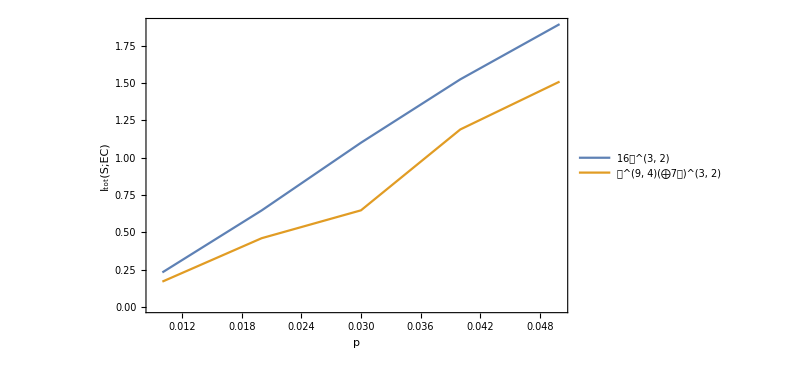

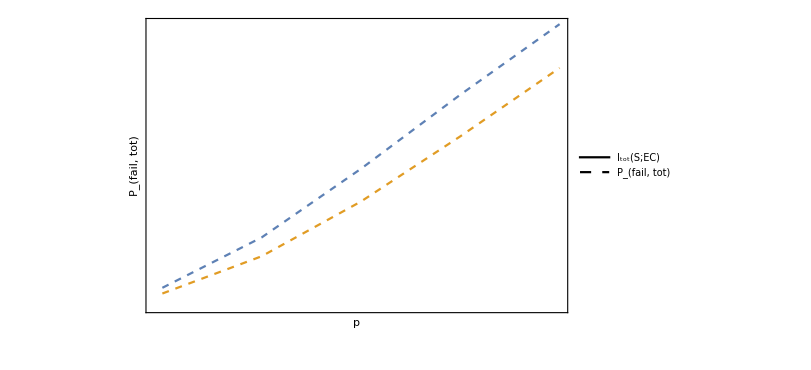

-Graphics--Graphics-

k16.pdf

{{{0.01,0.231496},{0.02,0.646416},{0.03,1.09971},{0.04,1.52383},{0.05,1.89326}},{{0.01,0.169866},{0.02,0.460474},{0.03,0.647073},{0.04,1.18837},{0.05,1.50862}},{{0.01,0.0629314},{0.02,0.202683},{0.03,0.4079},{0.04,0.646551},{0.05,0.919899}},{{0.01,0.0734723},{0.02,0.259011},{0.03,0.570635},{0.04,0.997908},{0.05,1.52738}}}

{{{0.01,0.0375097},{0.02,0.136038},{0.03,0.270304},{0.04,0.415113},{0.05,0.553128}},{{0.01,0.0263459},{0.02,0.0992262},{0.03,0.206279},{0.04,0.333705},{0.05,0.467492}},{{0.01,0.0148547},{0.02,0.0621702},{0.03,0.143042},{0.04,0.252195},{0.05,0.379996}},{{0.01,0.0107942},{0.02,0.0466095},{0.03,0.112109},{0.04,0.209678},{0.05,0.336778}}}

{{{0.01,0.231496},{0.02,0.646416},{0.03,1.09971},{0.04,1.52383},{0.05,1.89326}},{{0.01,0.169866},{0.02,0.460474},{0.03,0.647073},{0.04,1.18837},{0.05,1.50862}}}

{{{0.01,0.0629314},{0.02,0.202683},{0.03,0.4079},{0.04,0.646551},{0.05,0.919899}},{{0.01,0.0734723},{0.02,0.259011},{0.03,0.570635},{0.04,0.997908},{0.05,1.52738}}}

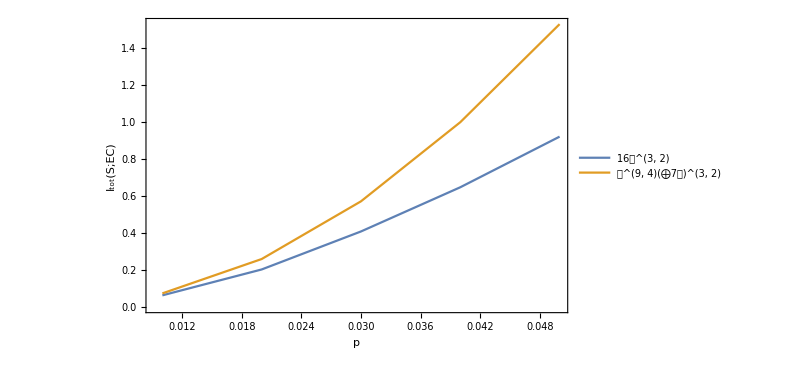

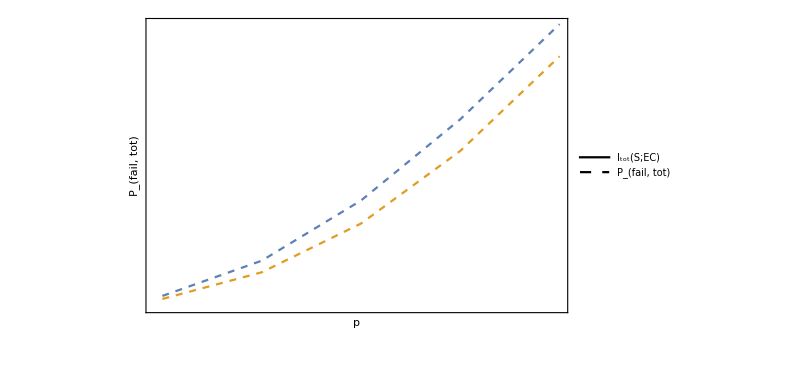

-Graphics--Graphics-

k16_2.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
s=Import["k16.csv"]
sNames=s[[1]]
sData=s[[2;;]]
DataPlot=Partition[Transpose[{sData[[;;,2]],sData[[;;,3]]}],5]
DataPlotPfail=Partition[Transpose[{sData[[;;,2]],sData[[;;,4]]}],5]
dataI1=DataPlot[[1;;2,;;]]
dataI2=DataPlot[[3;;4,;;]]
plot1=ListLinePlot[DataPlot[[1;;2,;;]],Frame->{True,True,True,False},ImagePadding->50,PlotLegends->Placed[{"16𝒞^(3, 2)","𝒞^(9, 4)(:2a017𝒞)^(3, 2)"},{0.1,0.8}],FrameLabel->{{"I_tot(S;EC)",None},{"p",None}},ImageSize->600]
plot2=ListLinePlot[DataPlotPfail[[1;;2,;;]],AxesLabel->{"p","P_(fail, tot)"},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},ImagePadding->50,PlotStyle->Dashed,FrameLabel->{{None,"P_(fail, tot)"},{None,None}},PlotLegends->Placed[LineLegend[{Black,{Dashed,Black}},{"I_tot(S;EC)","P_(fail, tot)"}],{0.12,0.6}],ImageSize->600] 
plot3=Overlay[{plot1,plot2}]
Export["k16.pdf",plot3]

DataPlot=Partition[Transpose[{sData[[;;,2]],sData[[;;,3]]}],5]
DataPlotPfail=Partition[Transpose[{sData[[;;,2]],sData[[;;,4]]}],5]
dataI1=DataPlot[[1;;2,;;]]
dataI2=DataPlot[[3;;4,;;]]
plot1=ListLinePlot[DataPlot[[3;;4,;;]],Frame->{True,True,True,False},ImagePadding->50,PlotLegends->Placed[{"16𝒞^(3, 2)","𝒞^(9, 4)(:2a017𝒞)^(3, 2)"},{0.1,0.8}],FrameLabel->{{"I_tot(S;EC)",None},{"p",None}},ImageSize->600]
plot2=ListLinePlot[DataPlotPfail[[3;;4,;;]],AxesLabel->{"p","P_(fail, tot)"},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},ImagePadding->50,PlotStyle->Dashed,FrameLabel->{{None,"P_(fail, tot)"},{None,None}},PlotLegends->Placed[LineLegend[{Black,{Dashed,Black}},{"I_tot(S;EC)","P_(fail, tot)"}],{0.12,0.6}],ImageSize->600] 
plot3=Overlay[{plot1,plot2}]
Export["k16_2.pdf",plot3]
```